```mathematica
oscillator[d_,w0_,x_]:=Module[{w, phi, A, cos, exp,y},
w=Sqrt[w0^2-d^2];
phi=ArcTan[-d/w];
A=1/(2*Cos[phi]);
cos=Cos[w0*x+phi];
exp=Exp[-d*x];
y=exp*2*A*cos;
y//N
]
```

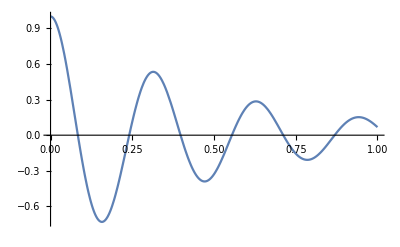

```mathematica
Plot[oscillator[2,20,x],{x,0,1}]
```

```mathematica
net[ninput_,noutput_,nhidden_,nlayers_]:=NetChain[{
nhidden,
FunctionLayer[Tanh],
Table[{
LinearLayer[nhidden],FunctionLayer[Tanh]},
{nlayers}],
LinearLayer[noutput], 

}]
```

```mathematica
data=Table[{x,oscillator[2,20,x]},{x,0,0.5,0.05}];
traindata =Thread[#[[1]]-> #[[2]]]&/@ data;
traindata = RandomChoice[traindata, Length[traindata]]
```

{0.35→0.407166,0.25→0.113595,0.→1.,0.45→-0.353598,0.1→-0.26589,0.2→-0.489136,0.45→-0.353598,0.4→-0.0206987,0.4→-0.0206987,0.→1.,0.05→0.565409}

```mathematica
data=Table[{x,oscillator[2,20,x]},{x,0,1,0.1}];
```

```mathematica
testdata =Thread[#[[1]]-> #[[2]]]&/@ data;
testdata = RandomChoice[testdata, Length[testdata]]
```

{0.3→0.511541,1.→0.0676455,0.6→0.237921,0.5→-0.328791,0.→1.,0.6→0.237921,0.9→0.0966733,0.7→0.0582701,1.→0.0676455,1.→0.0676455,0.8→-0.19919}

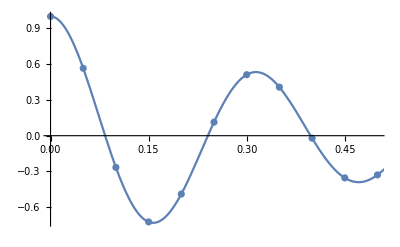

```mathematica
Show[
ListPlot[data],
Plot[oscillator[2,20,x],{x,0,1}]
]
```

```mathematica
firstnet=net[11,1,10,1]
```

NetChain[<>]

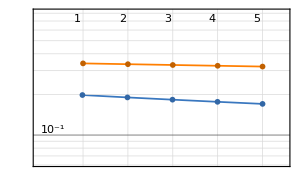
{NetChain[<>],NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5  rounds:5  time:2.3s  examples/s:24.
data | ,,  training examples:11  validation examples:11  processed examples:55  skipped examples:0
method | ,,  ADAMoptimizer  batch size11GPU
round | ,,  loss:3.22×10^-1
validation | ,,  loss:1.7×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]}

```mathematica
trainedfirstnet = NetTrain[firstnet,traindata,{"TrainedNet", "ResultsObject"}, TargetDevice->"GPU",MaxTrainingRounds->5, ValidationSet->testdata ]
```

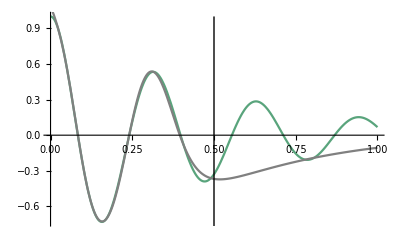

```mathematica
Show[
Plot[oscillator[2,20,x],{x,0,1}, ColorFunction->Hue],
Plot[trainedfirstnet[[1]][i], {i,0,1}, PlotStyle->Gray],
Graphics@Line[{{0.5, -1}, {0.5, 1}}]
]
```

```mathematica
PacletInstall["https://github.com/ssmit1986/DualNumbers/releases/download/1.2/DualNumbers-1.2.paclet"]
```

PacletObject[…]

```mathematica
<<DualNumbers`
```

```mathematica
SetDirectory [NotebookDirectory[]]
```

/home/s/Documents/wis22

```mathematica
Export[ "net.wlnet",trainedfirstnet[[1]]]
```

net.wlnet

```mathematica
net1 = Import["net.wlnet"]
```

NetChain[<>]

```mathematica
gradient[x_]:= (net1[x+10^-8]- net1[x] )/ 10^-8
```

```mathematica
ploss[inputs_, labels_]:= SquaredEuclideanDistance[inputs, labels]+ gradient[inputs]+gradient[gradient[inputs]]
```

SetDelayed::write: Tag Function in (gradient[#input,1/10^9]&)[inputs_,labels_] is Protected.

$Failed

```mathematica
net2 =NetGraph[{10, FunctionLayer[Tanh], 10, FunctionLayer[Tanh], 1, ploss}, {1->2->3->4->5}]
```

NetGraph::netinvnodes: gradient[#input,1/10^9]& is not a layer, a net, or a valid specification for one.

$Failed

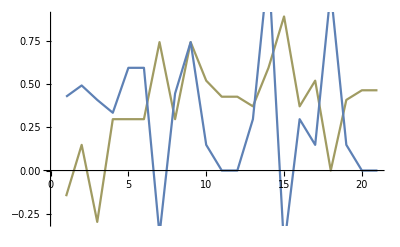
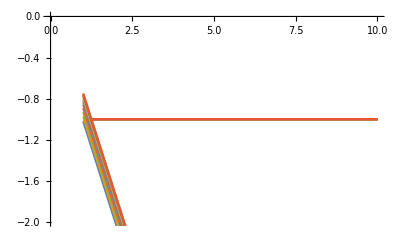
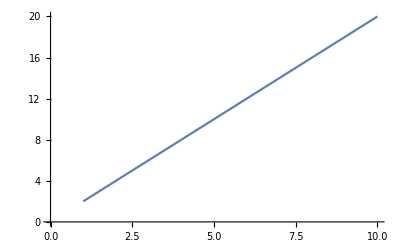
```mathematica
Show[
ListLinePlot[gradient[gradient[Range[0,1,0.05],10^-7, net1], 10^-7, net1], ColorFunction->"Rainbow"],
ListLinePlot@gradient[Range[0,1,0.05],10^-7, net1]
]
-Graphics-
gradient[Range[0,1,0.1],10^-9]
{2.0041607300267078*^7,-2.500867841127062*^7,-6.819188587998927*^7,-1.0771303613143414*^8,-1.424170284039163*^8,-1.7181862873538506*^8,-1.959740070529045*^8,-2.1530021705555093*^8,-2.3040693975296098*^8,-2.4196828877570903*^8,-2.5063845490187314*^8}
x =Range[0, 1, 0.1]
{0.,0.1,0.2,0.30000000000000004,0.4,0.5,0.6000000000000001,0.7000000000000001,0.8,0.9,1.}
Show[
ListLinePlot[NonStandard[f[Dual[Range[10],Table[1,10]]]]],
ListLinePlot[Standard[f[Dual[Range[10],Table[1,10]]]]]]
-Graphics-
f@Dual[Range[10],Table[1,10]]
Dual[{1,2,3,4,5,6,7,8,9,10},{1,1,1,1,1,1,1,1,1,1}]
f[a_]:= a^2 
ListLinePlot@NonStandard@f[Dual[Range[1,10], Table[1, 10]], ]
-Graphics-
g[x_,y_]:=x^2 * y^3;
d=NonStandard@g[Dual[a,1],Dual[b,1]]//Simplify
a b^2 (3 a+2 b)
Total@Grad[g[a, b], {a,b}] 
3 a^2 b^2+2 a b^3
```